```mathematica
(* 
This is a numerical code that can be used to calculate the sphaleron configuration(including the saddle-point field configuration and the sphaleron energy) using the spectral method. 

The general strategies can be summarized as the following steps:
(1) Choose the number of grid points and construct the Chebyshev differentiation matrix;
  (2) Shift the profile functions to satisfy the boundary conditions of the Chebyshev spectral method;
  (3) Work out the equations of motion of the shifted profile functions;
  (4) Calculate the derivatives at grid points using the differentiation matrix constructed in step (1);
  (5) Solve the algebraic equations with respective to the shifted profile functions at grid points; 
  (6) Shift back to obtain the profile functions, which correspond to the sphaleron field configuration;
  (7) Perform the numerical integral with the profile functions obtained in step (6). This gives the sphaleron energy.

For more details, please see arXiv: 2307.04713;
  Any comments or improvements about the code are welcome, please contact bingrongyu123@gmail.com;
  Below are two examples about the calculations of the sphaleron in the Standard Model and in the Higgs Triplet Model. 
*)
```

## Sphaleron in the Standard Model

```mathematica
(*The sphaleron configuration in the Standard Model depends on one parameter ρ1=λ/g^2*)
(* To calculate the sphaleron configuration in the Standard Model,please run the function SphaleronSM *)
```

### Sphaleron configuration calculated using the spectral method

```mathematica
Clear["Global`*"]
SphaleronSM[ρ1_]:=(For[energySM=10;count=0,energySM>3&&count<10,count++,
n=60;(*number of grid points*)
a=30;(*cut-off of the sphaleron distance parameter ξ*)
(*n and a can be adjusted. Basically, to evaluate the sphaleron configuration with large ρ1 more accurately, one should increase n and decrease a*)


(*Chebyshev grid points*)
Do[x[j]=N[Cos[j π/n]],{j,0,n}];
xx=Table[x[j],{j,1,n-1}];

(*construction of the Chebyshev differentiation matrix*)
u[0,0]=(2 n^2+1)/6;
u[0,n]=(1/2)(-1)^n;
u[n,0]=-(1/2)(-1)^n;
u[n,n]=-((2 n^2+1)/6);
Do[u[0,j]=(2(-1)^j)/(1-x[j]),{j,1,n-1}];
Do[u[n,j]=(-2(-1)^(n+j))/(1+x[j]),{j,1,n-1}];
Do[u[i,0]=-(1/2)((-1)^i/(1-x[i])),{i,1,n-1}];
Do[u[i,n]=(1/2)((-1)^(n+i)/(1+x[i])),{i,1,n-1}];
Do[u[j,j]=(-x[j])/(2(1-x[j]^2)),{j,1,n-1}];
Do[If[i≠j,u[i,j]=(-1)^(i+j)/(x[i]-x[j])],{i,1,n-1},{j,1,n-1}];
Diff=N[Table[u[i,j],{i,0,n},{j,0,n}]]; 
Diffcore=Table[Diff[[i,j]],{i,2,n},{j,2,n}]; 
Diffsq=N[Diff.Diff];
Diffsqcore=Table[Diffsq[[i,j]],{i,2,n},{j,2,n}];

(*calculating derivatives at grid points by the differentiation matrix*)
ff={Table[f[j],{j,1,n-1}]}//Transpose;
hh={Table[h[j],{j,1,n-1}]}//Transpose;
fp=Table[(Diffcore.ff)[[j]],{j,1,n-1}];
fpp=Table[(Diffsqcore.ff)[[j]],{j,1,n-1}];
hp=Table[(Diffcore.hh)[[j]],{j,1,n-1}];
hpp=Table[(Diffsqcore.hh)[[j]],{j,1,n-1}];

(*EOM of the shifted profile functions in the SM*)
eq1=2(1+xx)^2 fpp==(2ff+1+xx)(2ff-1+xx)(2ff+xx)+(a^2/16)(1+xx)^2(2ff-1+xx)(2hh+1+xx)^2;
eq2=(1+xx)^2 hpp+(1+xx)(2hp+1)==(1/4 )(2ff-1+xx)^2(2hh+1+xx)-((a^2 ρ1)/8)(1+xx)^2(2hh+1+xx)(4-(2hh+1+xx)^2);
eq=Join[Thread[eq1],Thread[eq2]];

(*solve the EOM of the shifted profile functions at grid points*)
var=Join[Table[{f[j],RandomReal[{0.9,1}]},{j,1,n-1}],Table[{h[j],RandomReal[{0.9,1}]},{j,1,n-1}]];
sol=Table[var[[i,1]],{i,1,2(n-1)}]/.FindRoot[eq,var];
fsol=Insert[Insert[sol[[;;n-1]],0,-1],0,1];
hsol=Insert[Insert[sol[[n;;]],0,-1],0,1];
fdata=Table[{x[j],fsol[[j+1]]},{j,0,n}];
hdata=Table[{x[j],hsol[[j+1]]},{j,0,n}];
d=2n;
ffit=Fit[fdata,Table[x^(i),{i,0,d}],x];
hfit=Fit[hdata,Table[x^(i),{i,0,d}],x];

(*shift back to obtain the profile functions*)
f0=(ffit+(1+x)/2)//Simplify;
h0=(hfit+(1+x)/2)//Simplify;
f0p=D[f0,x];
f0pp=D[f0,{x,2}];
h0p=D[h0,x];
h0pp=D[h0,{x,2}];
f=f0/.{x->ξ/a-1};
h=h0/.{x->ξ/a-1};


(*sphalron energy in the SM*)
energySM=NIntegrate[a((4/a^2)f0p^2+(8/(a^2(1+x)^2))f0^2(1-f0)^2+(1-f0)^2 h0^2+(1/2)(1+x)^2 h0p^2+(ρ1/4)a^2(1+x)^2(1-h0^2)^2),{x,-Cos[π/n],Cos[π/n]}]];
)
```

### Sphaleron energy and profile functions

```mathematica
(*in units of 4πv/g = 4.8 TeV *)
```

```mathematica
SphaleronSM[0.306];energySM
```

1.9173

```mathematica
(*profile functions*)
```

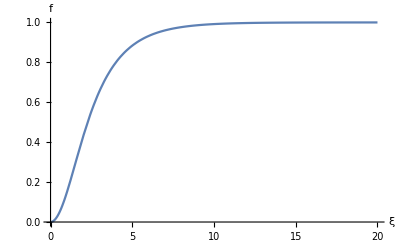

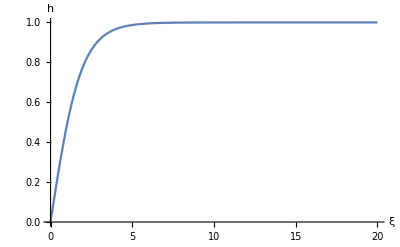

```mathematica
Plot[{f},{ξ,0,20},PlotRange->Full,AxesLabel->{"ξ","f"}]
Plot[{h},{ξ,0,20},PlotRange->Full,AxesLabel->{"ξ","h"}]
```

## Sphaleron in the Higgs Triplet Model

```mathematica
(* The sphaleron configuration in the Higgs Triplet Model depends on five parameters: ρ1=λ/g^2; ρ2=2λΔ^2/g^2;ρ3=vΔ^2/vϕ^2; ρ4=κ^2/(g^2 vϕ^2);ρ5=MΔ^2/(g^2 vϕ^2) *)
```

```mathematica
(* To calculate the sphaleron configuration in the Higgs Triplet Model,please run the function SphaleronHTM *)
```

### Sphaleron configuration calculated using the spectral method

```mathematica
Clear["Global`*"]
SphaleronHTM[ρ1_,ρ2_,ρ3_,ρ4_,ρ5_]:=(For[energyHTM=10;count=0,energyHTM>3&&count<10,count++,
β=1+2ρ3;
n=60;(*number of grid points*)
a=30;(*cut-off of the sphaleron distance parameter ξ*)
(*n and a can be adjusted. Basically, to evaluate the sphaleron configuration with large ρ1 more accurately, one should increase n and decrease a*)


(*Chebyshev grid points*)
Do[x[j]=N[Cos[j π/n]],{j,0,n}];
xx=Table[x[j],{j,1,n-1}];

(*construction of the Chebyshev differentiation matrix*)
u[0,0]=(2 n^2+1)/6;
u[0,n]=(1/2)(-1)^n;
u[n,0]=-(1/2)(-1)^n;
u[n,n]=-((2 n^2+1)/6);
Do[u[0,j]=(2(-1)^j)/(1-x[j]),{j,1,n-1}];
Do[u[n,j]=(-2(-1)^(n+j))/(1+x[j]),{j,1,n-1}];
Do[u[i,0]=-(1/2)((-1)^i/(1-x[i])),{i,1,n-1}];
Do[u[i,n]=(1/2)((-1)^(n+i)/(1+x[i])),{i,1,n-1}];
Do[u[j,j]=(-x[j])/(2(1-x[j]^2)),{j,1,n-1}];
Do[If[i≠j,u[i,j]=(-1)^(i+j)/(x[i]-x[j])],{i,1,n-1},{j,1,n-1}];
Diff=N[Table[u[i,j],{i,0,n},{j,0,n}]]; 
Diffcore=Table[Diff[[i,j]],{i,2,n},{j,2,n}]; 
Diffsq=N[Diff.Diff];
Diffsqcore=Table[Diffsq[[i,j]],{i,2,n},{j,2,n}];

(*calculating the derivatives at grid points using the differentiation matrix*)
ff={Table[f[j],{j,1,n-1}]}//Transpose;
hh={Table[h[j],{j,1,n-1}]}//Transpose;
hhd={Table[hd[j],{j,1,n-1}]}//Transpose;
fp=Table[(Diffcore.ff)[[j]],{j,1,n-1}];
fpp=Table[(Diffsqcore.ff)[[j]],{j,1,n-1}];
hp=Table[(Diffcore.hh)[[j]],{j,1,n-1}];
hpp=Table[(Diffsqcore.hh)[[j]],{j,1,n-1}];
hdp=Table[(Diffcore.hhd)[[j]],{j,1,n-1}];
hdpp=Table[(Diffsqcore.hhd)[[j]],{j,1,n-1}];

(*EOM of the shifted profile functions in the HTM*)
eq1=2(1+xx)^2 fpp==(2ff+1+xx)(2ff-1+xx)(2ff+xx)+(a^2/(16β))(1+xx)^2(2ff-1+xx)(2hh+1+xx)^2+((a^2 ρ3)/(6β))(1+xx)^2(2ff-1+xx)(2hhd+1+xx)^2;
eq2=(1+xx)^2 hpp+(1+xx)(2hp+1)==(1/4)(2ff-1+xx)^2(2hh+1+xx)-( a^2/(8β))(1+xx)^2((ρ1-ρ2)(2hh+1+xx)(4-(2hh+1+xx)^2)-ρ2(2hh+1+xx)((2hh+1+xx)^2-2(2hhd+1+xx))+4(ρ4-ρ1+ρ2)(2hh+1+xx)+2(√(2ρ2 ρ3 ρ5)-ρ2)(2hh+1+xx)(2hhd+1+xx)+(ρ1-ρ4-√(2ρ2 ρ3 ρ5))(2hh+1+xx)(2hhd+1+xx)^2);
eq3=ρ3(1+xx)^2 hdpp+ρ3(1+xx)(2hdp+1)==((2ρ3)/3)(2ff-1+xx)^2(2hhd+1+xx)-((a^2 ρ2)/(8β))(1+xx)^2((2hh+1+xx)^2-2(2hhd+1+xx))+(a^2/(8β))(1+xx)^2(2(2ρ3 ρ5-ρ2)(2hhd+1+xx)-(√(2ρ2 ρ3 ρ5)-ρ2)(2hh+1+xx)^2-(ρ1-ρ4-√(2ρ2 ρ3 ρ5))(2hh+1+xx)^2(2hhd+1+xx)+(ρ1-ρ4-ρ3 ρ5-√(ρ2 ρ3 ρ5/2))(2hhd+1+xx)^3);
eq=Join[Thread[eq1],Thread[eq2],Thread[eq3]];

(*solve the EOM of the shifted profile functions at grid points*)
var=Join[Table[{f[j],RandomReal[{0.9,1}]},{j,1,n-1}],Table[{h[j],RandomReal[{0.9,1}]},{j,1,n-1}],Table[{hd[j],RandomReal[{0.9,1}]},{j,1,n-1}]];
sol=Table[var[[i,1]],{i,1,3(n-1)}]/.FindRoot[eq,var];
fsol=Insert[Insert[sol[[;;n-1]],0,-1],0,1];
hsol=Insert[Insert[sol[[n;;2(n-1)]],0,-1],0,1];
hdsol=Insert[Insert[sol[[2n-1;;3(n-1)]],0,-1],0,1];
fdata=Table[{x[j],fsol[[j+1]]},{j,0,n}];
hdata=Table[{x[j],hsol[[j+1]]},{j,0,n}];
hddata=Table[{x[j],hdsol[[j+1]]},{j,0,n}];
d=2n;
ffit=Fit[fdata,Table[x^(i),{i,0,d}],x];
hfit=Fit[hdata,Table[x^(i),{i,0,d}],x];
hdfit=Fit[hddata,Table[x^(i),{i,0,d}],x];

(*shift back to obtain the profile functions*)
f0=(ffit+(1+x)/2)//Simplify;
h0=(hfit+(1+x)/2)//Simplify;
hd0=(hdfit+(1+x)/2)//Simplify;
f0p=D[f0,x];
h0p=D[h0,x];
hd0p=D[hd0,x];
f=f0/.{x->ξ/a-1};
h=h0/.{x->ξ/a-1};
hd=f0/.{x->ξ/a-1};


(*sphalron energy in the HTM*)
energyHTM=a NIntegrate[(4/a^2)f0p^2+(8/(a^2(1+x)^2))f0^2(1-f0)^2+(1/β)(1-f0)^2 h0^2+(1/(2 β))(1+x)^2 h0p^2+(1/(4 β^2))a^2(1+x)^2((ρ1-ρ2)(1-h0^2)^2+ρ2 (h0^2-hd0)^2)+(ρ3/(6β))(3(1+x)^2 hd0p^2+16 hd0^2(1-f0)^2)+((a^2(1+x)^2)/(4 β^2))(2(ρ4-ρ1+ρ2)(1-h0^2)-(2ρ3 ρ5-ρ2)(1-hd0^2))+((a^2(1+x)^2)/(2 β^2))(√(2ρ2 ρ3 ρ5)-ρ2)(1-h0^2 hd0)+((a^2(1+x)^2)/(2 β^2))(ρ1-ρ4-√(2ρ2 ρ3 ρ5))(1-h0^2 hd0^2)-((a^2(1+x)^2)/(4 β^2))(ρ1-ρ4-ρ3 ρ5-√(ρ2 ρ3 ρ5/2))(1-hd0^4),{x,-Cos[π/n],Cos[π/n]}]];
);
```

### Sphaleron energy and profile functions

```mathematica
(*in units of 4πv/g = 4.8 TeV *)
```

```mathematica
SphaleronHTM[0.6,0.01,10^-3,0.59,0.15];energyHTM
```

1.9972

```mathematica
(*profile functions*)
```

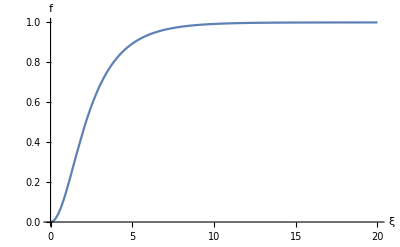

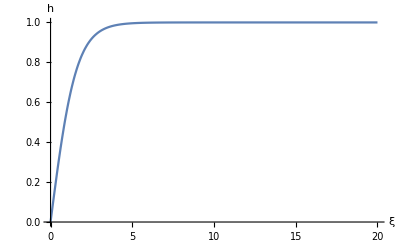

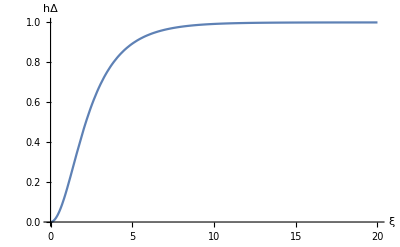

```mathematica
Plot[{f},{ξ,0,20},PlotRange->Full,AxesLabel->{"ξ","f"}]
Plot[{h},{ξ,0,20},PlotRange->Full,AxesLabel->{"ξ","h"}]
Plot[{hd},{ξ,0,20},PlotRange->Full,AxesLabel->{"ξ","hΔ"}]
```